```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
map4[x_,y_,μ_]=ComplexExpand[map[Re[map3[x,y,μ]],Im[map3[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
z = x+I y
map[z_,μ_]= ComplexExpand[μ (z)(1-(z))]
```

x+ⅈ y

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
ComplexPlot3D[map[z,3.8284],{z,0 + 0I,0.5 + 0.1I}]
```

-Graphics3D-

```mathematica
mor[x_,y_,μ_]=ComplexExpand[x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)-(μ/4+y^2 μ)+1/2]
```

1/2-μ/4+x μ-x^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
x = 1/6;
listpointsL = {};
j=1;
For[μ = 1, μ<4,μ=μ+0.01(*0.0000003*),
x = 0.51;
(*For[i=1,i<100,i++,
x = μ x(1-x)
];*)
AppendTo[listpointsL,{μ}];
For[i=1,i<100,i++,
x =(*μ x(1-x);*)1/2-μ/4+x μ-x^2 μ;
AppendTo[listpointsL⟦j⟧,x-1/2];
];
j++;
]
Clear[x,μ];
```

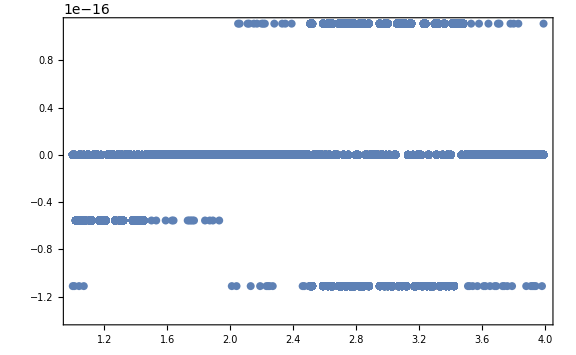

```mathematica
Pmor=ListPlot[TemporalData[listpointsL⟦All,2;;⟧,{listpointsL⟦All,1⟧}],PlotStyle->Directive[RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.01]],Frame->True,ImageSize->Large,PlotRange->Automatic]
```

```mathematica
mor[1/2,y,μ]
```

1/2

```mathematica
Solve[μ x (1-x)==x, x]/. μ-> 2
```

{{x→0},{x→1/2}}

```mathematica
Solve[1/2-μ/4+x μ-x^2 μ==x,x]
```

{{x→1/2},{x→(-2+μ)/(2 μ)}}

```mathematica
FullSimplify[(y μ-2 x y μ)]
```

(1-2 x) y μ

```mathematica
FullSimplify[(y μ-2 x y μ)]
```

(1-2 x) y μ

```mathematica
ComplexExpand[map[1/2,y,μ]]
```

μ/4+y^2 μ

```mathematica
lista={};
For[mu=3.8,mu≤ 3.83,mu=mu+0.01,
For[xis=0,xis≤ 1,xis=xis+0.05,
For [ips=-0.1,ips≤ 0.1,ips=ips+0.001,
AppendTo[lista,{Re[map[xis,ips,mu]],Im[map2[xis,ips,mu]],xis}]
]; 
];
];
```

```mathematica
ListPlot3D[lista,PlotStyle]
```

```mathematica
ParametricPlot[{{x,x},{x,Re[map[x,0,3.8]]},{x,Re[map2[x,0,3.8]]},{x,Re[map3[x,0,3.8]]},{x,Re[map4[x,0,3.8]]},{x,Re[map5[x,0,3.8]]},{x,Re[map6[x,0,3.8]]},{x,Re[map3[map4[x,0,3.8],0,3.8]]}},{x,0.4,0.6},Frame->True,GridLines->Automatic]
```

$Aborted

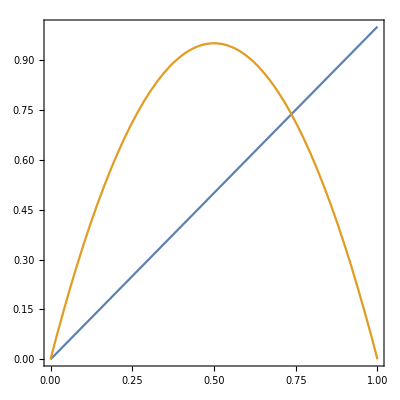

```mathematica
ParametricPlot[{{x,x},{x,Re[map[x,0,3.8]]}},{x,0,1},Frame->True]
```

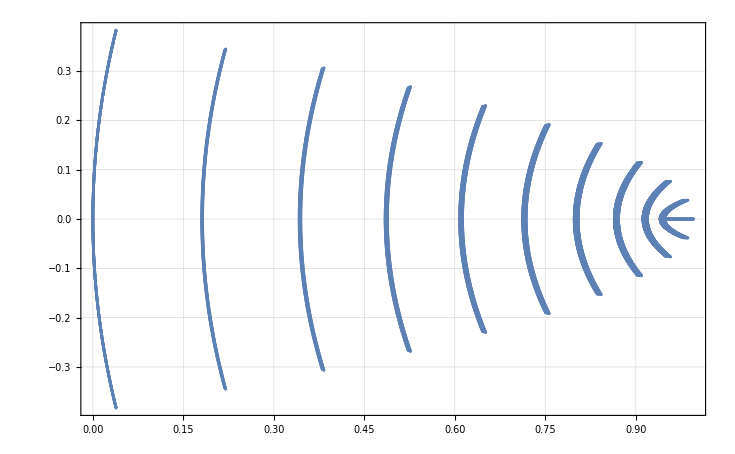

```mathematica
ListPlot[lista⟦All,1;;3;;2⟧,Frame->True,GridLines->Automatic]
```

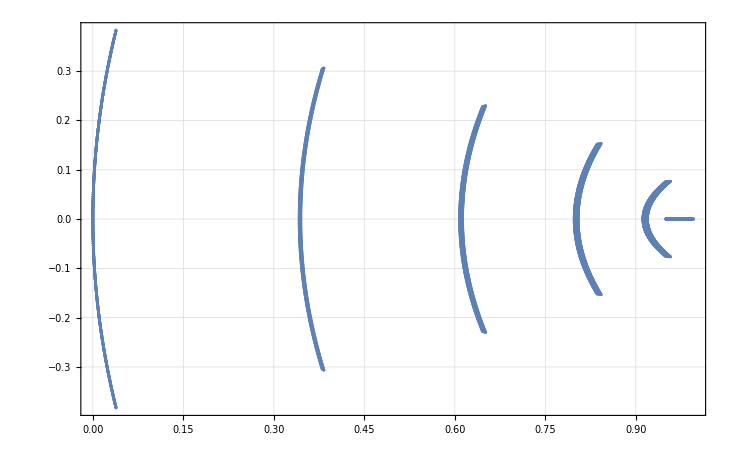

```mathematica
lista
```

{{0.389224,3.9,-0.30888},{0.388456,3.9,-0.30576},{0.387695,3.9,-0.30264},{0.386942,3.9,-0.29952},{0.386197,3.9,-0.2964},2201,{-0.392305,3.9,-0.45396},{-0.391544,3.9,-0.45864},{-0.390776,3.9,-0.46332},{-0.39,3.9,-0.468},{-0.389216,3.9,-0.47268}}
 |  |  |  |

3.8

```mathematica
expression = x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
ComplexExpand[Re[expression]]
```

x μ-x^2 μ+y^2 μ

```mathematica
(*imaginary = (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7);
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;*)
```

```mathematica
mu1 = Range[3,3.8,0.01];
complexmap ={}
For[i=0,i< Length[mu1],i++;
μ1 = mu1⟦i⟧;
xc =0.5;
yc = 0.05;
For[j=0,j<5,j++;
{xc,yc} = {ComplexExpand[Re[map[xc,yc,μ1]]],ComplexExpand[Im[map[xc,yc,μ1]]]};
AppendTo[complexmap,{μ1,xc,Chop[yc]}]]]4
```

{}

```mathematica
map4[0.5,0.01,3.82]
```

0.953356-1.7405×10^-11 ⅈ

```mathematica
complexmap;
```

```mathematica
ListPointPlot3D[complexmap,PlotRange->{Automatic,Automatic,{-0.005,0.005}}]
```

-Graphics3D-

```mathematica
re1=Normal[Series[Simplify[Re[map3[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]]
im1=Normal[Series[Simplify[Im[map3[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]]
```

μ^3 (x-2 x^5 (-3-2 μ) μ^3+4 x^7 μ^4-x^8 μ^4-2 x^6 μ^3 (1+3 μ)-x^2 (1+μ+μ^2)+2 x^3 μ (1+μ+μ^2)-x^4 μ (1+μ+6 μ^2+μ^3))+y^2 μ^3 (1+μ+μ^2-84 x^5 μ^4+28 x^6 μ^4-6 x μ (1+μ+μ^2)+2 x^3 μ (-30 μ^2-20 μ^3)+30 x^4 μ (μ^2+3 μ^3)+6 x^2 (μ+μ^2+6 μ^3+μ^4))

2 (-1+2 x) y^3 μ^3 (μ+μ^2+μ^3-10 x μ^3+10 x^2 μ^3-2 x μ^4+16 x^2 μ^4-28 x^3 μ^4+14 x^4 μ^4)+(-1+2 x) y μ^3 (-1+12 x^5 μ^4-4 x^6 μ^4+2 x μ (1+μ)+4 x^3 μ^3 (3+μ)-2 x^4 μ^3 (3+6 μ)-2 x^2 μ (1+μ+3 μ^2))

```mathematica
s=Solve[im1==0,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→1/2},{y→0},{y→-((√(1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))/(√2 √(μ+μ^2+μ^3-10 x μ^3+10 x^2 μ^3-2 x μ^4+16 x^2 μ^4-28 x^3 μ^4+14 x^4 μ^4)))},{y→(√(1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))/(√2 √(μ+μ^2+μ^3-10 x μ^3+10 x^2 μ^3-2 x μ^4+16 x^2 μ^4-28 x^3 μ^4+14 x^4 μ^4))}}

```mathematica
Block[{μ=3.8284},NSolve[{re1==x,im1==y},{x,y},Reals]]
```

{{x→0.956319,y→0.00014036},{x→0.956319,y→-0.000138772},{x→0.738794,y→0.},{x→0.514356,y→0.00126975},{x→0.514356,y→-0.00126975},{x→0.15993,y→0.000487634},{x→0.15993,y→-0.000487635},{x→0.,y→0.}}

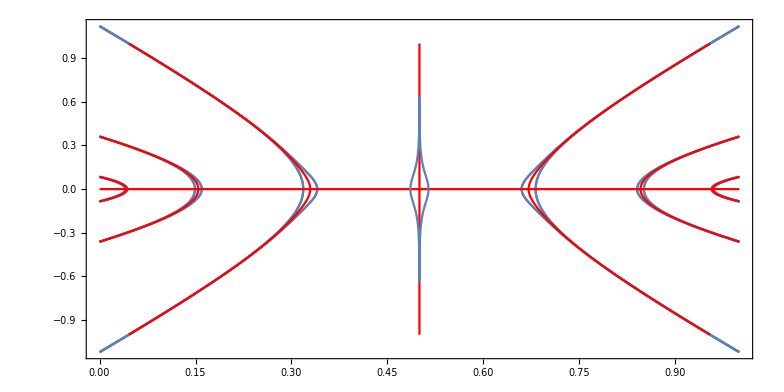
```mathematica
bands=-Graphics-;
```

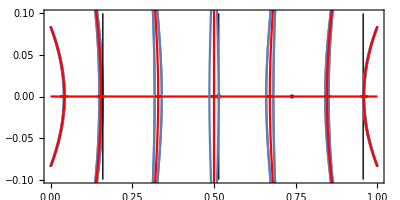

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{0.738794,0}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,0.00048763427602524213}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,-0.00048763427602524213}]}],
Graphics[{Line[{{0.15993001243546456,-0.1},{0.15993001243546456,0.1}}]}],
Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,0.0012697462828370391}]}],Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,-0.0012697462828370391}]}],Graphics[{PointSize[Large],Line[{{0.5143556522364481,-0.1},{0.5143556522364481,0.1}}]}],
Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,0.0001403599703116611}]}],Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,-0.0001403599703116611}]}],Graphics[{PointSize[Large],Line[{{0.9563189850083437,-0.1},{0.9563189850083437,0.1}}]}],
bands,Frame-> True,AspectRatio-> 1/2,PlotRange->{{0,1}, {-0.1,0.1}}]
```

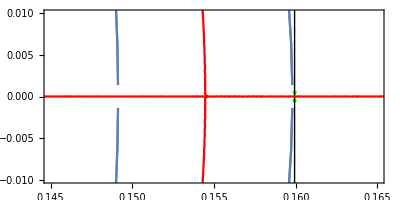

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{0.738794,0}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,0.00048763427602524213}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,-0.00048763427602524213}]}],
Graphics[{Line[{{0.15993001243546456,-0.1},{0.15993001243546456,0.1}}]}],
Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,0.0012697462828370391}]}],Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,-0.0012697462828370391}]}],Graphics[{PointSize[Large],Line[{{0.5143556522364481,-0.1},{0.5143556522364481,0.1}}]}],
Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,0.0001403599703116611}]}],Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,-0.0001403599703116611}]}],Graphics[{PointSize[Large],Line[{{0.9563189850083437,-0.1},{0.9563189850083437,0.1}}]}],
bands,Frame-> True,AspectRatio-> 1/2,PlotRange->{{0.145,0.165}, {-0.01,0.01}}]
```

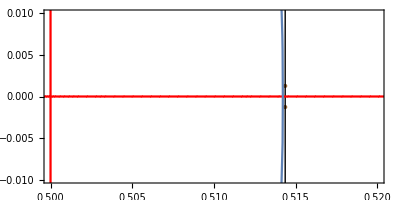

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{0.738794,0}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,0.00048763427602524213}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,-0.00048763427602524213}]}],
Graphics[{Line[{{0.15993001243546456,-0.1},{0.15993001243546456,0.1}}]}],
Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,0.0012697462828370391}]}],Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,-0.0012697462828370391}]}],Graphics[{PointSize[Large],Line[{{0.5143556522364481,-0.1},{0.5143556522364481,0.1}}]}],
Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,0.0001403599703116611}]}],Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,-0.0001403599703116611}]}],Graphics[{PointSize[Large],Line[{{0.9563189850083437,-0.1},{0.9563189850083437,0.1}}]}],
bands,Frame-> True,AspectRatio-> 1/2,PlotRange->{{0.5,0.52}, {-0.01,0.01}}]
```

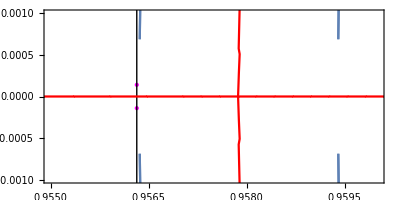

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{0.738794,0}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,0.00048763427602524213}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,-0.00048763427602524213}]}],
Graphics[{Line[{{0.15993001243546456,-0.1},{0.15993001243546456,0.1}}]}],
Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,0.0012697462828370391}]}],Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,-0.0012697462828370391}]}],Graphics[{PointSize[Large],Line[{{0.5143556522364481,-0.1},{0.5143556522364481,0.1}}]}],
Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,0.0001403599703116611}]}],Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,-0.0001403599703116611}]}],Graphics[{PointSize[Large],Line[{{0.9563189850083437,-0.1},{0.9563189850083437,0.1}}]}],
bands,Frame-> True,AspectRatio-> 1/2,PlotRange->{{0.955,0.96}, {-0.001,0.001}}]
```

```mathematica
cloud1=-Graphics-;
```

```mathematica
Show[Graphics[{PointSize[Large],Blue,Point[{0.738794,0}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,0.00048763427602524213}]}],
Graphics[{PointSize[Large],Green,Point[{0.15993001243546456,-0.00048763427602524213}]}],
Graphics[{Line[{{0.15993001243546456,-0.1},{0.15993001243546456,0.1}}]}],
Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,0.0012697462828370391}]}],Graphics[{PointSize[Large],Brown,Point[{0.5143556522364481,-0.0012697462828370391}]}],Graphics[{PointSize[Large],Line[{{0.5143556522364481,-0.1},{0.5143556522364481,0.1}}]}],
Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,0.0001403599703116611}]}],Graphics[{PointSize[Large],Magenta,Point[{0.9563189850083437,-0.0001403599703116611}]}],Graphics[{PointSize[Large],Line[{{0.9563189850083437,-0.1},{0.9563189850083437,0.1}}]}],
bands,
cloud1,
Frame-> True,AspectRatio-> 1,PlotRange->{{0.156,0.16}, {-0.002,0.002}}]
```

-Graphics-

```mathematica
band1pts = {};
up =maxvalues⟦1⟧;
For[i=0,i<3000,i++;
px= RandomReal[{0,up}];
If[px<minvalues⟦1⟧,pmax = Re[f1max[px]];pmin = Re[f1min[px]], 
pmax=Re[f1max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band1pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.000104357} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000138673} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000390216} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
s⟦3,1,2⟧
FullSimplify[re1/. x-> s⟦3,1,2⟧]
```

-((√(1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))/(√2 √(μ+μ^2+μ^3-10 x μ^3+10 x^2 μ^3-2 x μ^4+16 x^2 μ^4-28 x^3 μ^4+14 x^4 μ^4)))

$Aborted

```mathematica
re11=Normal[Series[Simplify[Re[map[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]]
im11=Normal[Series[Simplify[Im[map[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]]
```

(x-x^2) μ+y^2 μ

(1-2 x) y μ

```mathematica
x01 = Solve[im1==0,y]⟦All,1⟧
```

{y→0,y→-(√(-1+2 x) √(1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))/(√(-2 μ+4 x μ-2 μ^2+4 x μ^2-2 μ^3+24 x μ^3-60 x^2 μ^3+40 x^3 μ^3+4 x μ^4-40 x^2 μ^4+120 x^3 μ^4-140 x^4 μ^4+56 x^5 μ^4)),y→(√(-1+2 x) √(1-2 x μ+2 x^2 μ-2 x μ^2+2 x^2 μ^2+6 x^2 μ^3-12 x^3 μ^3+6 x^4 μ^3-4 x^3 μ^4+12 x^4 μ^4-12 x^5 μ^4+4 x^6 μ^4))/(√(-2 μ+4 x μ-2 μ^2+4 x μ^2-2 μ^3+24 x μ^3-60 x^2 μ^3+40 x^3 μ^3+4 x μ^4-40 x^2 μ^4+120 x^3 μ^4-140 x^4 μ^4+56 x^5 μ^4))}

```mathematica
re12=Normal[Series[Simplify[Re[map2[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]]
im12=Normal[Series[Simplify[Im[map2[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]]
```

```mathematica
re13=Normal[Series[Simplify[Re[map3[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]];
im13=Normal[Series[Simplify[Im[map3[x,y,μ]], Assumptions->{x∈ Reals,y∈ Reals, μ ∈ Reals}],{y,0,3}]];
```

```mathematica
x03 = Solve[map3[x,y,μ]==0,y]⟦All,1⟧
```

{y→ⅈ (-1+x),y→ⅈ x,y→1/2 (-ⅈ+2 ⅈ x-√(-1-(2 √(-4+μ))/μ^(3/2)+2/μ)),y→1/2 (-ⅈ+2 ⅈ x+√(-1-(2 √(-4+μ))/μ^(3/2)+2/μ)),y→1/2 (-ⅈ+2 ⅈ x-√(-1+(2 √(-4+μ))/μ^(3/2)+2/μ)),y→1/2 (-ⅈ+2 ⅈ x+√(-1+(2 √(-4+μ))/μ^(3/2)+2/μ)),y→-(ⅈ μ-2 ⅈ x μ-√(4 μ-μ^2))/(2 μ),y→-(ⅈ μ-2 ⅈ x μ+√(4 μ-μ^2))/(2 μ)}

```mathematica
Chop[x03⟦7⟧/.{μ ->3.8284 ,y-> 0}]
```

x→0.845539

```mathematica
x02 = Solve[im12==0,x]⟦All,1⟧
```

{x→1/2,x→(μ-√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ),x→(μ+√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)}

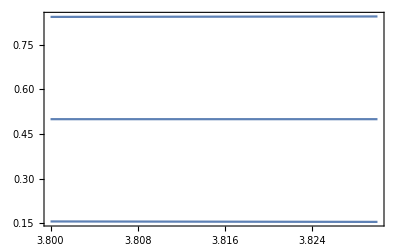

```mathematica
Plot[x02⟦All,2⟧/.y-> 0,{μ,3.8,3.83},Frame->True]
```

```mathematica
x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7/.μ-> 3.8284/. y-> 0/.x-> 0.5
```

0.507198

```mathematica
x02⟦3⟧/. y-> 0/. μ-> 3.8384
```

x→0.846031

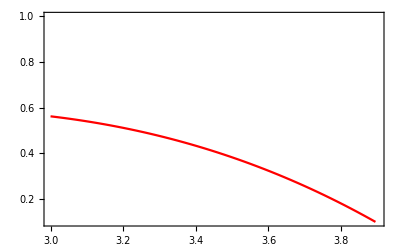

```mathematica
Show[Plot[map[re12/. x-> x02⟦3,2⟧/. y-> 0,0,μ],{μ,3.,3.9},Frame->True,PlotRange->{0.1,1.0},PlotStyle->Red]]
```

```mathematica
ListPlot[{xpos22⟦5,All,1;;2⟧/.y-> 0},PlotRange-> {{3,3.9},Automatic}]
```

-Graphics-

```mathematica
x0=Solve[im1==0,x]⟦All,1⟧ (* Valores de x que levam y para 0. Note que são INdependentes de y (em ordem 1)*);
```

```mathematica
x0⟦7⟧;
```

```mathematica
Plot3D[x0⟦7,2⟧,{μ,3.8,3.83},{y,-0.1,0.1}];
```

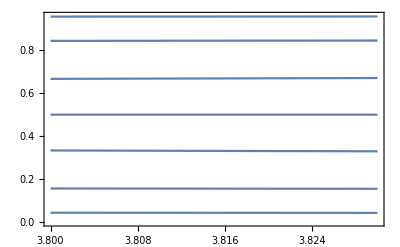

```mathematica
Plot[x0⟦All,2⟧/.y-> 0,{μ,3.8,3.83},Frame->True]
```

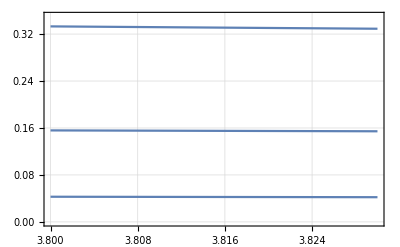

```mathematica
Plot[x0⟦All,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True,PlotRange->{0,0.35},GridLines->Automatic]
```

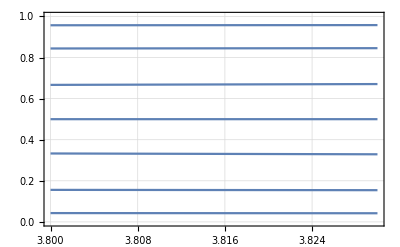

```mathematica
Plot[x0⟦All,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True,PlotRange->{0,1.0},GridLines->Automatic]
```

```mathematica
xpos= {};
j=0;
For[mu=3.,mu≤ 3.93,mu=mu+0.001,
j++;
For[i=1,i≤ Length[x0],i++,
xpos=AppendTo[xpos,{mu,Chop[re1/.x0⟦i⟧/.μ-> mu],y}];
]
]
(* Novos valores de x, que terão y=0 (em odem 1). Devem ser os pontos de acúmulo! Note que eles dependem do valor anterior de y (e, claro, de μ)!*)
```

$Aborted

```mathematica
xpos2= {};
For[i=1,i≤ Length[x0],i++,
xposlocal={};
For[mu=3.,mu≤ 3.93,mu=mu+0.01,
AppendTo[xposlocal, {mu,Chop[re1/.x0⟦i⟧/.μ-> mu],y}];
];
AppendTo[xpos2,xposlocal]]
```

```mathematica
xpos2⟦1⟧
```

{{3.,0.738281+1.6875 y^2,y},{3.01,0.741448+1.66897 y^2,y},{3.02,0.744621+1.64702 y^2,y},{3.03,0.747796+1.62151 y^2,y},{3.04,0.750972+1.59228 y^2,y},{3.05,0.754146+1.55915 y^2,y},{3.06,0.757316+1.52198 y^2,y},{3.07,0.760479+1.48057 y^2,y},{3.08,0.763633+1.43477 y^2,y},{3.09,0.766774+1.38438 y^2,y},{3.1,0.7699+1.32924 y^2,y},{3.11,0.773007+1.26914 y^2,y},{3.12,0.776092+1.20389 y^2,y},{3.13,0.779152+1.1333 y^2,y},{3.14,0.782183+1.05716 y^2,y},{3.15,0.785181+0.975269 y^2,y},{3.16,0.788143+0.887408 y^2,y},{3.17,0.791064+0.793363 y^2,y},{3.18,0.79394+0.692909 y^2,y},{3.19,0.796766+0.585819 y^2,y},{3.2,0.799539+0.471859 y^2,y},{3.21,0.802253+0.350792 y^2,y},{3.22,0.804904+0.222372 y^2,y},{3.23,0.807486+0.0863509 y^2,y},{3.24,0.809994-0.0575269 y^2,y},{3.25,0.812423-0.209522 y^2,y},{3.26,0.814766-0.369902 y^2,y},{3.27,0.817018-0.538937 y^2,y},{3.28,0.819174-0.716908 y^2,y},{3.29,0.821226-0.904097 y^2,y},{3.3,0.823168-1.1008 y^2,y},{3.31,0.824994-1.3073 y^2,y},{3.32,0.826696-1.52391 y^2,y},{3.33,0.828267-1.75094 y^2,y},{3.34,0.829701-1.98871 y^2,y},{3.35,0.830989-2.23753 y^2,y},{3.36,0.832124-2.49773 y^2,y},{3.37,0.833097-2.76965 y^2,y},{3.38,0.833901-3.05364 y^2,y},{3.39,0.834526-3.35004 y^2,y},{3.4,0.834964-3.6592 y^2,y},{3.41,0.835207-3.9815 y^2,y},{3.42,0.835243-4.31729 y^2,y},{3.43,0.835065-4.66697 y^2,y},{3.44,0.834662-5.03091 y^2,y},{3.45,0.834024-5.40951 y^2,y},{3.46,0.83314-5.80316 y^2,y},{3.47,0.832001-6.21228 y^2,y},{3.48,0.830594-6.63728 y^2,y},{3.49,0.828909-7.07858 y^2,y},{3.5,0.826935-7.53662 y^2,y},{3.51,0.824659-8.01184 y^2,y},{3.52,0.822069-8.50467 y^2,y},{3.53,0.819152-9.01559 y^2,y},{3.54,0.815897-9.54505 y^2,y},{3.55,0.812289-10.0935 y^2,y},{3.56,0.808316-10.6615 y^2,y},{3.57,0.803963-11.2495 y^2,y},{3.58,0.799217-11.8579 y^2,y},{3.59,0.794063-12.4874 y^2,y},{3.6,0.788486-13.1383 y^2,y},{3.61,0.782472-13.8113 y^2,y},{3.62,0.776004-14.5069 y^2,y},{3.63,0.769067-15.2256 y^2,y},{3.64,0.761644-15.968 y^2,y},{3.65,0.753719-16.7346 y^2,y},{3.66,0.745275-17.526 y^2,y},{3.67,0.736295-18.3428 y^2,y},{3.68,0.726761-19.1856 y^2,y},{3.69,0.716654-20.055 y^2,y},{3.7,0.705956-20.9517 y^2,y},{3.71,0.694649-21.8761 y^2,y},{3.72,0.682712-22.829 y^2,y},{3.73,0.670126-23.8111 y^2,y},{3.74,0.656871-24.8228 y^2,y},{3.75,0.642926-25.8651 y^2,y},{3.76,0.628269-26.9384 y^2,y},{3.77,0.61288-28.0436 y^2,y},{3.78,0.596737-29.1812 y^2,y},{3.79,0.579816-30.3521 y^2,y},{3.8,0.562095-31.5569 y^2,y},{3.81,0.543551-32.7964 y^2,y},{3.82,0.524159-34.0713 y^2,y},{3.83,0.503896-35.3823 y^2,y},{3.84,0.482737-36.7303 y^2,y},{3.85,0.460656-38.1161 y^2,y},{3.86,0.437627-39.5403 y^2,y},{3.87,0.413624-41.0039 y^2,y},{3.88,0.38862-42.5077 y^2,y},{3.89,0.362588-44.0524 y^2,y},{3.9,0.3355-45.6389 y^2,y},{3.91,0.307327-47.2682 y^2,y},{3.92,0.278041-48.9409 y^2,y},{3.93,0.247612-50.6582 y^2,y}}

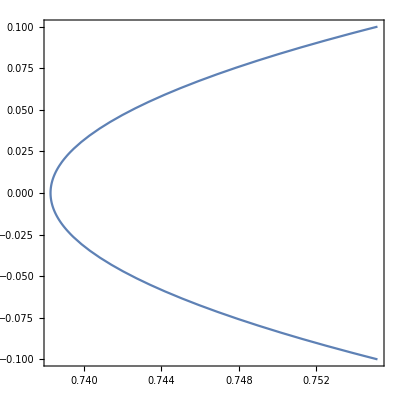
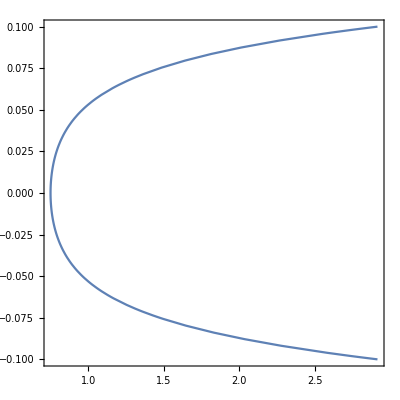
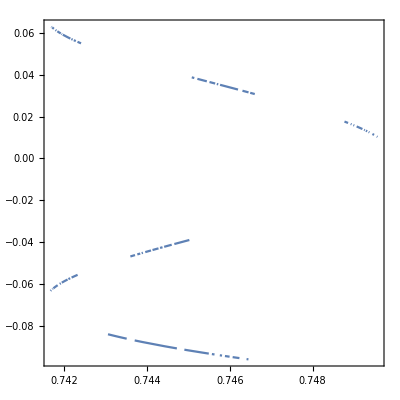
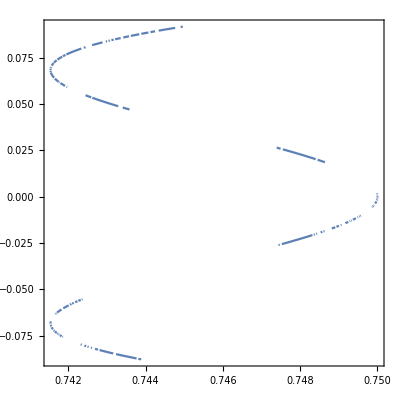
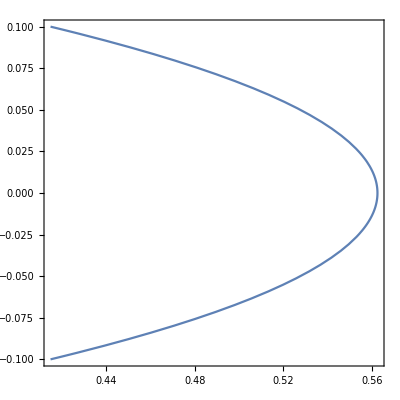
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ParametricPlot[xpos2⟦i,1,2;;3⟧,{y,-0.1,0.1},Frame->True,AspectRatio->1],{i,1,7}]
```

```mathematica
ParametricPlot[xpos⟦2,2;;3⟧,{y,-0.1,0.1},Frame->True,AspectRatio->1]
```

O Plot abaixo compara curvas que não possuem o mesmo valor de μ, e que podem se referir a um mesmo valor de x0. São parametric  lots feitos para os índices de 1 a 6000 com passo 1000 de xpos, sendo que xpos percorre os 7 x0’s disponíveis com um mesmo valor de μ para que possa passar para o próximo

```mathematica
ParametricPlot[xpos⟦1;;6000;;1000,2;;3⟧,{y,-0.1,0.1},Frame->True,AspectRatio->1]
```

$Aborted

```mathematica
ParametricPlot[xpos⟦2000,2;;3⟧,{y,-0.1,0.1},Frame->True,AspectRatio->1]
```

$Aborted

```mathematica
Length[xpos⟦6500⟧];
xpos⟦10⟧/.y-> 0
```

{3.001,0.75025+0. ⅈ,0}

```mathematica
ParametricPlot[xpos⟦1;;6517;;500,2;;3⟧,{y,-0.1,0.1},Frame->True,AspectRatio->1,PlotRange->{{0,0.3},Automatic}]
```

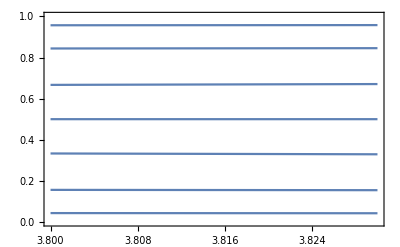

```mathematica
Plot[x0⟦All,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True,PlotRange->{0,1}]
```

```mathematica
Complx0⟦4,2⟧/. y-> 0
```

Part::partd: Part specification Complx0⟦4,2⟧ is longer than depth of object.

Complx0⟦4,2⟧

```mathematica
FullSimplify[Chop[x0⟦4,2⟧/. y-> 0./. μ-> 3.17]]
```

0.5-0.0596041 ⅈ

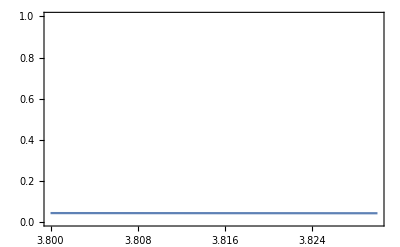

```mathematica
Plot[x0⟦2,2⟧/. y-> 0,{μ,3.8,3.83},Frame->True,PlotRange->{0,1}]
```

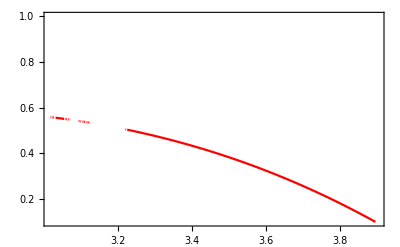

```mathematica
Show[Plot[map[re1/. x-> x0⟦4,2⟧/. y-> 0,0,μ],{μ,3.,3.9},Frame->True,PlotRange->{0.1,1.0},PlotStyle->Red]]
```

```mathematica
Show[Plot[map5[re1/. x-> x0⟦1,2⟧/. y-> 0,0,μ],{μ,3.,3.9},Frame->True,PlotRange->{0.1,1.0},PlotStyle->Red]]
```

$Aborted

```mathematica
singlecurves = {};
weightcurves = {};

AppendTo[singlecurves,{map[re1/. x-> x0⟦1,2⟧/. y-> 0,0,μ],map[re1/. x-> x0⟦2,2⟧/. y-> 0,0,μ],map[re1/. x-> x0⟦6,2⟧/. y-> 0,0,μ]}];
AppendTo[weightcurves,{1,4,2}];

AppendTo[singlecurves,{map2[re1/. x-> x0⟦1,2⟧/. y-> 0,0,μ],map2[re1/. x-> x0⟦2,2⟧/. y-> 0,0,μ],map2[re1/. x-> x0⟦6,2⟧/. y-> 0,0,μ]}];
AppendTo[weightcurves,{1,4,2}];

AppendTo[singlecurves,{map3[re1/. x-> x0⟦1,2⟧/. y-> 0,0,μ],map2[re1/. x-> x0⟦2,2⟧/. y-> 0,0,μ],map2[re1/. x-> x0⟦6,2⟧/. y-> 0,0,μ]}];
AppendTo[weightcurves,{1,4,2}];

AppendTo[singlecurves,{map4[re1/. x-> x0⟦1,2⟧/. y-> 0,0,μ],map4[re1/. x-> x0⟦2,2⟧/. y-> 0,0,μ],map4[re1/. x-> x0⟦6,2⟧/. y-> 0,0,μ]}];
AppendTo[weightcurves,{1,4,2}];

AppendTo[singlecurves,{map5[re1/. x-> x0⟦1,2⟧/. y-> 0,0,μ],map4[re1/. x-> x0⟦2,2⟧/. y-> 0,0,μ],map4[re1/. x-> x0⟦6,2⟧/. y-> 0,0,μ]}];
AppendTo[weightcurves,{1,4,2}];
```

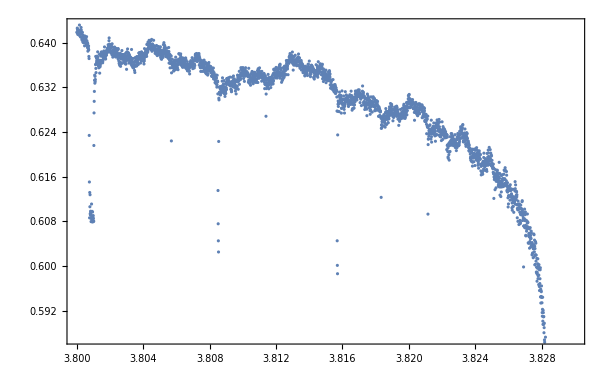
```mathematica
media = -Graphics-;
```

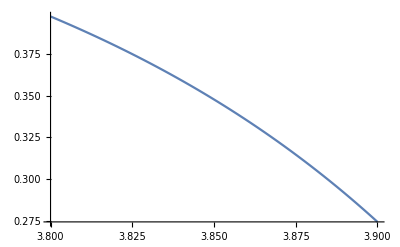

```mathematica
weighted1[μ_] =(singlecurves⟦1,1⟧ weightcurves ⟦1,1⟧+singlecurves⟦1,2⟧  weightcurves⟦1,2⟧+singlecurves⟦1,3⟧ weightcurves ⟦1,3⟧)/Total[weightcurves⟦1⟧];
weighted2[μ_] =(singlecurves⟦2,1⟧ weightcurves ⟦2,1⟧+singlecurves⟦2,2⟧  weightcurves⟦2,2⟧+singlecurves⟦2,3⟧ weightcurves ⟦2,3⟧)/Total[weightcurves⟦2⟧] ;
weighted3[μ_] =(singlecurves⟦3,1⟧ weightcurves ⟦3,1⟧+singlecurves⟦3,2⟧  weightcurves⟦3,2⟧+singlecurves⟦3,3⟧ weightcurves ⟦3,3⟧)/Total[weightcurves⟦3⟧];
weighted4[μ_] =(singlecurves⟦4,1⟧ weightcurves ⟦4,1⟧+singlecurves⟦4,2⟧  weightcurves⟦4,2⟧+singlecurves⟦4,3⟧ weightcurves ⟦4,3⟧)/Total[weightcurves⟦1⟧];
weighted5[μ_] =(singlecurves⟦5,1⟧ weightcurves ⟦5,1⟧+singlecurves⟦5,2⟧  weightcurves⟦5,2⟧+singlecurves⟦5,3⟧ weightcurves ⟦5,3⟧)/Total[weightcurves⟦2⟧];
Plot[weighted1[μ],{μ,3.8,3.9}]
```

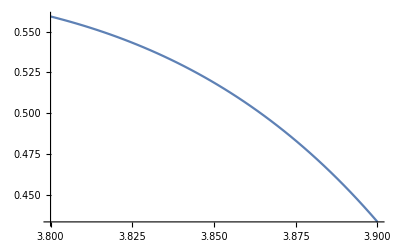

```mathematica
single1[μ_] =(singlecurves⟦1,1⟧ +singlecurves⟦1,2⟧  +singlecurves⟦1,3⟧)/3;
weighted2[μ_] =(singlecurves⟦2,1⟧ weightcurves ⟦2,1⟧+singlecurves⟦2,2⟧  weightcurves⟦2,2⟧+singlecurves⟦2,3⟧ weightcurves ⟦2,3⟧)/Total[weightcurves⟦2⟧] ;
weighted3[μ_] =(singlecurves⟦3,1⟧ weightcurves ⟦3,1⟧+singlecurves⟦3,2⟧  weightcurves⟦3,2⟧+singlecurves⟦3,3⟧ weightcurves ⟦3,3⟧)/Total[weightcurves⟦3⟧];
weighted4[μ_] =(singlecurves⟦4,1⟧ weightcurves ⟦4,1⟧+singlecurves⟦4,2⟧  weightcurves⟦4,2⟧+singlecurves⟦4,3⟧ weightcurves ⟦4,3⟧)/Total[weightcurves⟦1⟧];
weighted5[μ_] =(singlecurves⟦5,1⟧ weightcurves ⟦5,1⟧+singlecurves⟦5,2⟧  weightcurves⟦5,2⟧+singlecurves⟦5,3⟧ weightcurves ⟦5,3⟧)/Total[weightcurves⟦2⟧];
Plot[single1[μ],{μ,3.8,3.9}]
```

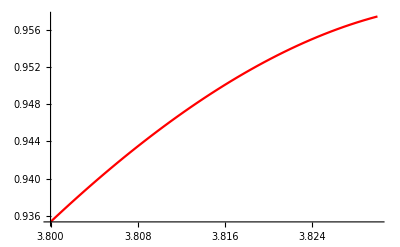

```mathematica
Plot[singlecurves⟦1,1⟧ , {μ,3.8,3.83}, PlotStyle->Red]
```

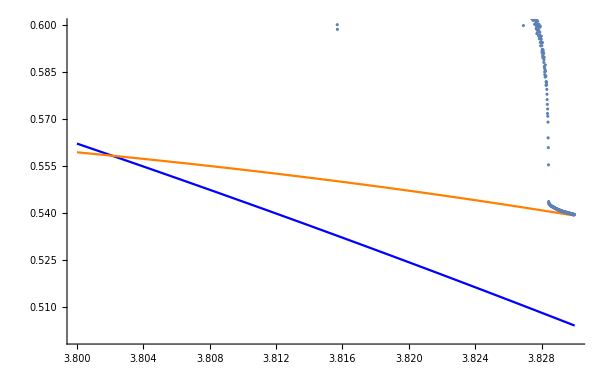

```mathematica
Show[
Plot[singlecurves⟦1,1⟧ , {μ,3.825,3.83}, PlotStyle->Red],
Plot[singlecurves⟦1,2⟧ , {μ,3.8,3.83}, PlotStyle->Green],
Plot[singlecurves⟦1,3⟧ , {μ,3.8,3.83}, PlotStyle->Blue],
Plot[single1[μ] , {μ,3.8,3.83}, PlotStyle->Orange],
media,
 PlotRange-> {0.5,0.6}]
```

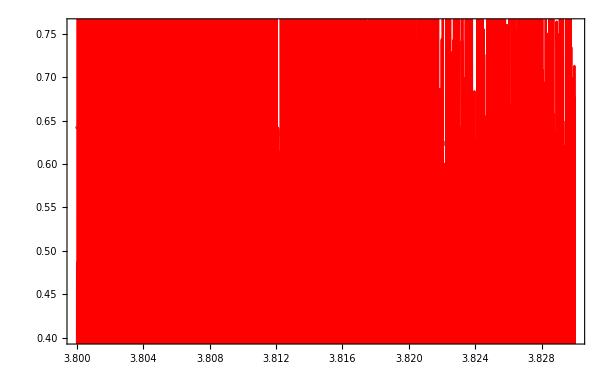

```mathematica
Show[media,Plot[(weighted1[μ]+ weighted2[μ]+ weighted3[μ] + weighted4[μ]+weighted5[μ])/5, {μ,3.800,3.83}, PlotStyle->Red], PlotRange-> {0.40,0.76}]
```

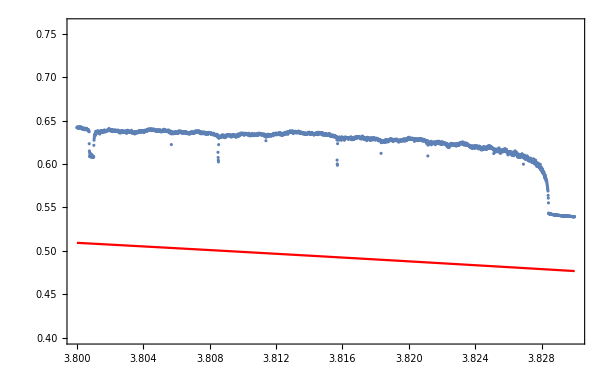

```mathematica
Show[media,Plot[(weighted1[μ]+weighted2[μ])/2, {μ,3.800,3.83}, PlotStyle->Red], PlotRange-> {0.40,0.76}]
```

```mathematica
x = 0.56;
listpointsL = {};
j=1;
For[μ = 3, μ<3.93,μ=μ+0.001(*0.0000003*),
(*For[i=1,i<100,i++,
x = μ x(1-x)
];*)
AppendTo[listpointsL,{μ}];
For[i=1,i<100,i++,
x =μ x(1-x);
AppendTo[listpointsL⟦j⟧,x];
];
j++;
]
Clear[x,μ];
```

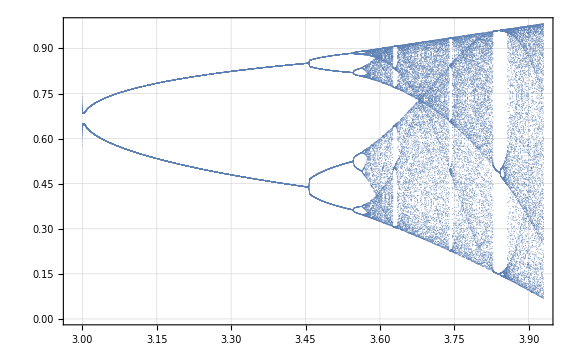

```mathematica
shadows=ListPlot[TemporalData[listpointsL⟦All,2;;⟧,{listpointsL⟦All,1⟧}],PlotStyle->Directive[RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.001]],Frame->True,GridLines->Automatic,ImageSize->Large]
```

```mathematica
lis0 = Table[{xpos[[i,1]],xpos⟦i,2⟧/.y -> 0},{i,1,Length[xpos]}];
```

```mathematica
lis = Table[{xpos[[i,1]],map[xpos⟦i,2⟧,0,xpos⟦i,1⟧]/.y -> 0},{i,1,Length[xpos]}];
```

```mathematica
lis2 = Table[{xpos[[i,1]],map2[xpos[[i,2]],0,xpos[[i,1]]]/.y -> 0},{i,1,Length[xpos]}];
```

```mathematica
lis3 = Table[{xpos[[i,1]],map3[xpos[[i,2]],0,xpos[[i,1]]]/.y -> 0},{i,1,Length[xpos]}];
```

```mathematica
lis4 = Table[{xpos[[i,1]],map[map3[xpos[[i,2]],0,xpos[[i,1]]],0,xpos[[i,1]]]/.y -> 0},{i,1,Length[xpos]}];
```

```mathematica
full=Show[ListPlot[{xpos⟦All,1;;2⟧/. y-> 0,lis,lis2,lis3,lis4},PlotStyle->{{PointSize[0.01],Green},{PointSize[0.005],Red},{PointSize[0.005],Brown},{PointSize[0.005],Yellow},{PointSize[0.005],Orange}},Frame->True],shadows,ImageSize-> Large]
```

-Graphics-

```mathematica
Show[full,PlotRange-> {{3.7,3.87},Automatic}]
```

-Graphics-

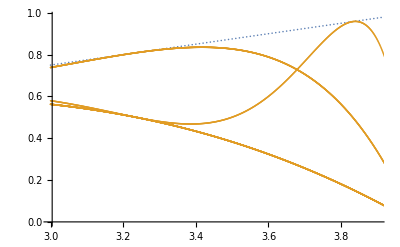

```mathematica
ListPlot[{xpos2⟦5,All,1;;2⟧/.y-> 0,lis},PlotRange-> {{3,3.9},Automatic}]
```

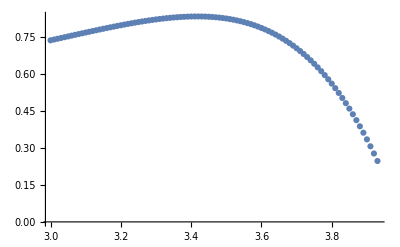

```mathematica
ListPlot[xpos2⟦1,All,1;;2⟧/.y-> 0]
```

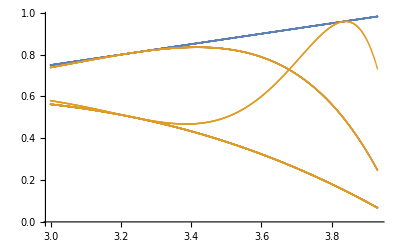

```mathematica
ListPlot[{lis0,lis}]
```

```mathematica
Length[xpos2⟦1⟧]
```

94

```mathematica
xpos2⟦1,All,1;;2⟧/.y-> 0
```

{{3.,0.738281},{3.01,0.741448},{3.02,0.744621},{3.03,0.747796},{3.04,0.750972},{3.05,0.754146},{3.06,0.757316},{3.07,0.760479},{3.08,0.763633},{3.09,0.766774},{3.1,0.7699},{3.11,0.773007},{3.12,0.776092},{3.13,0.779152},{3.14,0.782183},{3.15,0.785181},{3.16,0.788143},{3.17,0.791064},{3.18,0.79394},{3.19,0.796766},{3.2,0.799539},{3.21,0.802253},{3.22,0.804904},{3.23,0.807486},{3.24,0.809994},{3.25,0.812423},{3.26,0.814766},{3.27,0.817018},{3.28,0.819174},{3.29,0.821226},{3.3,0.823168},{3.31,0.824994},{3.32,0.826696},{3.33,0.828267},{3.34,0.829701},{3.35,0.830989},{3.36,0.832124},{3.37,0.833097},{3.38,0.833901},{3.39,0.834526},{3.4,0.834964},{3.41,0.835207},{3.42,0.835243},{3.43,0.835065},{3.44,0.834662},{3.45,0.834024},{3.46,0.83314},{3.47,0.832001},{3.48,0.830594},{3.49,0.828909},{3.5,0.826935},{3.51,0.824659},{3.52,0.822069},{3.53,0.819152},{3.54,0.815897},{3.55,0.812289},{3.56,0.808316},{3.57,0.803963},{3.58,0.799217},{3.59,0.794063},{3.6,0.788486},{3.61,0.782472},{3.62,0.776004},{3.63,0.769067},{3.64,0.761644},{3.65,0.753719},{3.66,0.745275},{3.67,0.736295},{3.68,0.726761},{3.69,0.716654},{3.7,0.705956},{3.71,0.694649},{3.72,0.682712},{3.73,0.670126},{3.74,0.656871},{3.75,0.642926},{3.76,0.628269},{3.77,0.61288},{3.78,0.596737},{3.79,0.579816},{3.8,0.562095},{3.81,0.543551},{3.82,0.524159},{3.83,0.503896},{3.84,0.482737},{3.85,0.460656},{3.86,0.437627},{3.87,0.413624},{3.88,0.38862},{3.89,0.362588},{3.9,0.3355},{3.91,0.307327},{3.92,0.278041},{3.93,0.247612}}

```mathematica
NotebookSave[EvaluationNotebook[]];
```

```mathematica
n=8;
L={};
For[i=38 300.,i≤ 384 30,i++,
μ=i/3000.;
For[j=1,j<10,j++,
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}},WorkingPrecision->MachinePrecision];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}},WorkingPrecision->MachinePrecision];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
]
]
L = DeleteDuplicates[L];
Clear[μ]
```

```mathematica
tab1=FindRoot[{Re[map3[x,y,3.80]]== x,Im[map3[x,y,3.80]]== y},{{x,0.7},{y,0.1}}];
(*tab1⟦2,2⟧
Round[tab1⟦2,2⟧10^8] 10^-8;*)
```

```mathematica
Lnum = {};
For[i=1,i<Length[L],i++,
AppendTo[Lnum,{L⟦i⟧,i}];]
(*AppendTo[Lnum⟦i⟧,i]]*)
```

```mathematica
afterw = Select[L,#⟦1⟧>3.8284 &];
beforew= Select[L, #⟦1⟧<3.8284 &];
```

```mathematica
pontos = L;
groupA = Select[pontos, #⟦2⟧<0.1 &];
groupBstep = Select[pontos, #⟦2⟧>0.1 &];
groupB = Select[groupBstep, #⟦2⟧<0.2 &];
groupCstep = Select[pontos, #⟦2⟧>0.4 &];
groupC= Select[groupCstep, #⟦2⟧<0.6 &];
groupDstep = Select[pontos, #⟦2⟧>0.6 &];
groupD = Select[groupDstep, #⟦2⟧<0.8 &];
groupE = Select[pontos, #⟦2⟧>0.8 &];
```

```mathematica
ListPointPlot3D[groupE]
```

-Graphics3D-

```mathematica
pontos⟦All,1;;2⟧
```

```mathematica
pf=ListPlot[pontos⟦All,1;;2⟧,PlotStyle->Red];
```

```mathematica
Show[full,pf]
```

Show::gcomb: Could not combine the graphics objects in Show[full,pf].

Show[full,pf]

```mathematica
Show[full,pf,PlotRange-> {{3.8,3.84},Automatic}]
```

-Graphics-

```mathematica
ptsf=Partition[Flatten[Table[Table[{x0⟦j,2⟧,0.01},{μ,3.8,3.84,0.01}],{j,1,Length[x0]}]],2];
```

```mathematica
Length[pontos]
```

0

```mathematica
ListPlot[{pontos⟦All,2;;3⟧,ptsf},Frame->True]
```

```mathematica
ListPlot[{pontos⟦All,2;;3⟧,ptsf},Frame->True,PlotRange->{{0.14,0.18},Automatic}]
```